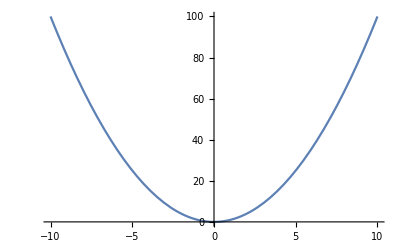

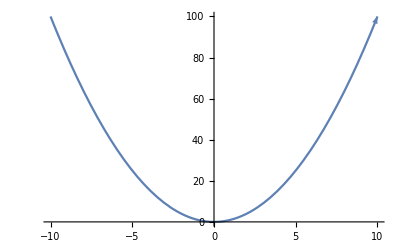

```mathematica
ClearAll[f,x,data];
f[x_]:=x^2;
data=Table[{x,f[x]},{x,-10,10,0.1}];
p0=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->{Blue,Thick}];

p0=Plot[x^2,{x,-10,10}]
p0/.Line[x_]:>{Arrowheads[Table[.05,{2}]],Arrow[x]}
```

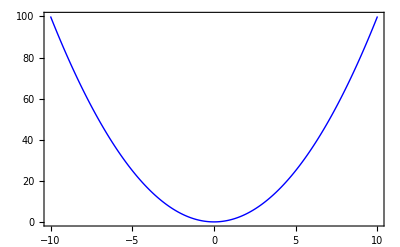

```mathematica
p0
```

```mathematica
Table[.05,{3}]
```

{0.05,0.05,0.05}

```mathematica
Graphics[{Arrowheads[{-.1,.1}],Arrow[{{0,0},{1,1/3}}]}]
```

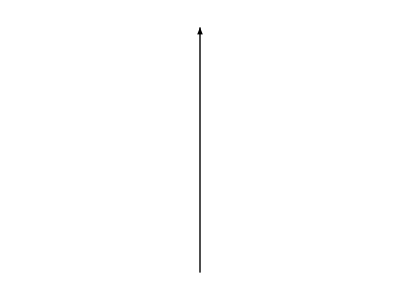

```mathematica
Graphics[{Arrowheads[Table[.02,{3}]],Arrow[{{0,2},{0,3}}]}]
```

```mathematica
Graphics[{Arrowheads[Table[.05,{3}]]}]
```

-Graphics-

```mathematica
p0//Hold
```

Hold[p0]

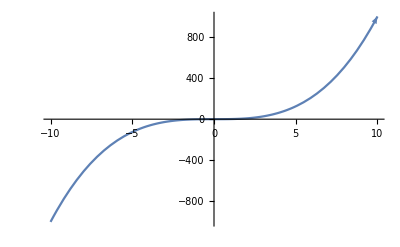

```mathematica
p0=Plot[x^3,{x,-10,10}];
p0/.Line[x_]:>{Arrowheads[Table[.05,{2}]],Arrow[x]}
```